```mathematica
$MinPrecision=53;
```

### General Parameters

```mathematica
IDFolderName="/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Source";
```

### Defining The Domains

#### u Domain(s)

u=1/r

```mathematica
prec=64;
```

```mathematica
uOuterMin=1/10;(*The boundary of the inner subdomain*)
uOuterMax= 11/10;(*The boundary of the last outer subdomain, should be close to the horizon*)
uOuterDomains=2;(*Number of outer subdomain*)
uOuterNodes=24;(*Number of points in each outer subdomains*)
uInnerNodes=12;(*Number of points in the inner subdomains*)
InterfaceNodes=Table[uOuterMin+i(uOuterMax-uOuterMin)/uOuterDomains,{i,0,uOuterDomains,1}];(*This gives the nodes where the subdomains meet*)
```

```mathematica
InterfaceNodes//N
```

{0.1,0.6,1.1}

The function below gives an array containing arrays.
Each of these arrays is a subdomain that contains its relative points.

```mathematica
(*GetuDomain[uOutMin_,uOutmax_,uOutDomains_,uOutNodes_,uInnNodes_,IntfaceNodes_]:=Module[{uu=uOutMin},
XInn=Table[-Cos[Pi i/(uInnNodes-1)],{i,0,uInnNodes-1}];
uInner=N[Table[(IntfaceNodes[[1]]+0)/2+(IntfaceNodes[[1]]-0)/2 XInn[[i]],{i,1,uInnNodes}],prec];
XOut=Table[-Cos[Pi i/(uOutNodes-1)],{i,0,uOutNodes-1}];
uOut=N[Flatten[Table[Table[1/2(IntfaceNodes[[j]]+IntfaceNodes[[j-1]])+1/2(IntfaceNodes[[j]]-IntfaceNodes[[j-1]])XOut[[i]],{i,2,uOutNodes}],{j,2,IntfaceNodes//Length}],1],prec];
Join[uInner,uOut]
]*)
```

```mathematica
GetuDomain2[uOutMin_,uOutmax_,uOutDomains_,uOutNodes_,uInnNodes_,IntfaceNodes_]:=Module[{uu=uOutMin},
XInn=Table[-Cos[Pi i/(uInnNodes-1)],{i,0,uInnNodes-1}];
uInner=N[Table[(IntfaceNodes[[1]]+0)/2+(IntfaceNodes[[1]]-0)/2 XInn[[i]],{i,1,uInnNodes}],prec];
XOut=Table[-Cos[Pi i/(uOutNodes-1)],{i,0,uOutNodes-1}];
uOut=N[Table[Table[1/2(IntfaceNodes[[j]]+IntfaceNodes[[j-1]])+1/2(IntfaceNodes[[j]]-IntfaceNodes[[j-1]])XOut[[i]],{i,1,uOutNodes}],{j,2,IntfaceNodes//Length}],prec];
(*Print[Flatten[uOut,{1}]//Dimensions];*)
Insert[Flatten[uOut,{1}],uInner,1]
]
```

```mathematica
(*uValues=(*{{0.0,0.002025351319275129,0.00793732335844094,0.017256963302735746,0.02922924934990568,0.042884258086335746,0.05711574191366425,0.07077075065009432,0.08274303669726425,0.09206267664155907,0.09797464868072488,0.1},{0.09999999999999998,0.10144367836436871,0.10574782046109107,0.11283224826665475,0.12256499229529424,0.1347647499408149,0.1492042628011086,0.1656145500721956,0.1836899191516714,0.2030936601134971,0.22346431797684174,0.244422425928476,0.265577574071524,0.2865356820231582,0.30690633988650284,0.3263100808483286,0.3443854499278044,0.36079573719889135,0.37523525005918507,0.38743500770470574,0.3971677517333452,0.4042521795389089,0.40855632163563127,0.41000000000000003},{0.41,0.4114436783643687,0.41574782046109104,0.4228322482666548,0.4325649922952942,0.4447647499408149,0.4592042628011086,0.47561455007219555,0.4936899191516714,0.5130936601134971,0.5334643179768417,0.5544224259284759,0.5755775740715239,0.5965356820231582,0.6169063398865028,0.6363100808483285,0.6543854499278043,0.6707957371988913,0.685235250059185,0.6974350077047056,0.7071677517333451,0.7142521795389087,0.7185563216356312,0.72},{0.72,0.7214436783643687,0.7257478204610911,0.7328322482666547,0.7425649922952943,0.7547647499408149,0.7692042628011087,0.7856145500721956,0.8036899191516714,0.8230936601134972,0.8434643179768417,0.864422425928476,0.8855775740715239,0.9065356820231583,0.9269063398865028,0.9463100808483286,0.9643854499278044,0.9807957371988913,0.9952352500591851,1.0074350077047056,1.0171677517333453,1.0242521795389088,1.0285563216356313,1.03}}*)GetuDomain2[uOuterMin,uOuterMax,uOuterDomains,uOuterNodes,uInnerNodes,InterfaceNodes];*)
```

I call the function GetuDomain to define my u-grid.

```mathematica
uValues=GetuDomain2[uOuterMin,uOuterMax,uOuterDomains,uOuterNodes,uInnerNodes,InterfaceNodes];
```

```mathematica
uValues
```

{{0,0.00202535131927513050548159714668361504687725757889190224777524705,0.007937323358440941556909417554031614124335375078973105067867494116,0.01725696330273574679715374637668532234081044003315357861968521977,0.02922924934990567872353629253851883982379975447677315937868883338,0.04288425808633574297781036656918151656044743194370078357909586067,0.05711574191366425702218963343081848343955256805629921642090413933,0.07077075065009432127646370746148116017620024552322684062131116662,0.08274303669726425320284625362331467765918955996684642138031478023,0.09206267664155905844309058244596838587566462492102689493213250588,0.09797464868072486949451840285331638495312274242110809775222475295,0.1},{0.1,0.102328513490917311914419259975948498715000204136293902334837174,0.109270678163050176246194100656690300161245385481663390206251837,0.1206971746236367455390486380085961265774264569471499458015451357,0.1363951488633778618629460951124372999880360912762768837128103458,0.1560721773238950482397247472576157761030693174190224698110976716,0.1793617141953364792813656136568648554753073106773333889114180113,0.2058299194712832146872379311832867940052809110084878793982673086,0.2349837405672119684896060600472620511105183832406375570598880579,0.2662800969572534620104712322880274606231447523721479849787392115,0.2991359967368415525304928194846053933055415832774757690094078661,0.3329393966588322560197028802443852440167271120702848065752896167,0.3670606033411677439802971197556147559832728879297151934247103833,0.4008640032631584474695071805153946066944584167225242309905921339,0.4337199030427465379895287677119725393768552476278520150212607885,0.4650162594327880315103939399527379488894816167593624429401119421,0.4941700805287167853127620688167132059947190889915121206017326914,0.5206382858046635207186343863431351445246926893226666110885819887,0.5439278226761049517602752527423842238969306825809775301889023284,0.5636048511366221381370539048875627000119639087237231162871896542,0.5793028253763632544609513619914038734225735430528500541984548643,0.590729321836949823753805899343309699838754614518336609793748163,0.597671486509082688085580740024051501284999795863706097665162826,0.6},{0.6,0.602328513490917311914419259975948498715000204136293902334837174,0.609270678163050176246194100656690300161245385481663390206251837,0.6206971746236367455390486380085961265774264569471499458015451357,0.6363951488633778618629460951124372999880360912762768837128103458,0.6560721773238950482397247472576157761030693174190224698110976716,0.6793617141953364792813656136568648554753073106773333889114180113,0.7058299194712832146872379311832867940052809110084878793982673086,0.7349837405672119684896060600472620511105183832406375570598880579,0.7662800969572534620104712322880274606231447523721479849787392115,0.7991359967368415525304928194846053933055415832774757690094078661,0.8329393966588322560197028802443852440167271120702848065752896167,0.8670606033411677439802971197556147559832728879297151934247103833,0.9008640032631584474695071805153946066944584167225242309905921339,0.9337199030427465379895287677119725393768552476278520150212607885,0.9650162594327880315103939399527379488894816167593624429401119421,0.9941700805287167853127620688167132059947190889915121206017326914,1.020638285804663520718634386343135144524692689322666611088581989,1.043927822676104951760275252742384223896930682580977530188902328,1.063604851136622138137053904887562700011963908723723116287189654,1.079302825376363254460951361991403873422573543052850054198454864,1.090729321836949823753805899343309699838754614518336609793748163,1.097671486509082688085580740024051501284999795863706097665162826,1.1}}

#### x Domain

```mathematica
xMin=-100000;
xMax=100000;
xNodes=64;
Deltax=Abs[xMin-xMax]/xNodes;
xValues=Table[xMin+i Deltax,{i,0,xNodes-1}];
```

```mathematica
xValues
```

{-100000,-96875,-93750,-90625,-87500,-84375,-81250,-78125,-75000,-71875,-68750,-65625,-62500,-59375,-56250,-53125,-50000,-46875,-43750,-40625,-37500,-34375,-31250,-28125,-25000,-21875,-18750,-15625,-12500,-9375,-6250,-3125,0,3125,6250,9375,12500,15625,18750,21875,25000,28125,31250,34375,37500,40625,43750,46875,50000,53125,56250,59375,62500,65625,68750,71875,75000,78125,81250,84375,87500,90625,93750,96875}

#### y Domain

```mathematica
yMin = xMin;
yMax = xMax;
yNodes = xNodes;
Deltay = Abs[yMin - yMax]/yNodes;
yValues = Table[yMin + i Deltay, {i, 0, yNodes - 1}];
```

#### Grid

Here I define the grid. The first entry is for the number relative to the subdomain,2nd entry is the u-point, 3rd and 4th are for the x and y point. The outpout is the triplet that represent the point in the grid.

```mathematica
MyGrid=Table[{uValues[[i,u]],xValues[[x]],yValues[[y]]},{i,1,uValues//Length},{u,1,uValues[[i]]//Length},{x,1,xValues//Length},{y,1,yValues//Length}];
```

```mathematica
MyGrid[[2,1,1,1]]//Dimensions
```

{3}

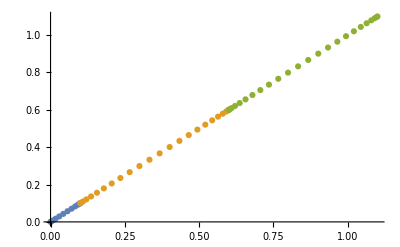

```mathematica
ListPlot[Table[{uValues[[i]],uValues[[i]]}//Transpose,{i,1,uValues//Length}]]
```

## Boosted Black Brain

## Homogeneous boosting

```mathematica
(*gdd=1/ρ^2 Table[ηdd[[u,v]]+,{u,1,4},{v,1,4}]*)
```

Here the goal is to intialise a boosted black brane in an inhomogeneous way, with noise created by a sum of sinusoidal functions each multiplied by small random coefficients

#### Boosting

```mathematica
ClearAll[u1d,u0d,u2d]
u1d[x_,y_]:= 0.01;
u2d[x_,y_]:=0;
b=1;
```

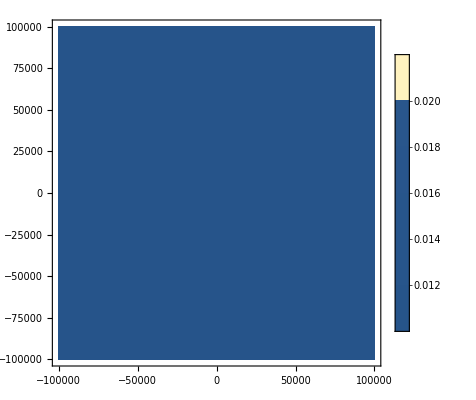

```mathematica
ContourPlot[u1d[x,y],{x,xMin,xMax},{y,yMin,yMax},PlotRange->All,PlotLegends->Automatic(*,ColorFunction->"TemperatureMap"*)(*,MaxRecursion->6*)(*,PlotPoints->20*)]
```

```mathematica
(*ClearAll[b]*)
```

Below I use the definition of u0d.

```mathematica
u0d[x_,y_]:=(*u2d[x,y]/.*)Solve[u1d[x,y]^2+u2d[x,y]^2-uu0d[x,y]^2==-1,uu0d[x,y]][[2,1,2]]
```

```mathematica
(*uofρ=NDSolve[{D[u[ρ],ρ]==(u[ρ]^2/ρ^2(1+(b ρ)^3(u1^2+u2^2))^(-1/2)),u[ϵ]==ϵ},u,{ρ,ϵ,1}][[1,1]];*)
```

```mathematica
(*ρofu=DSolve[{D[ρ[u,x,y],{u,1}]==(u^2/ρ[u,x,y]^2(1+(b ρ[u,x,y])^3(u1[x,y]^2+u2[x,y]^2))^(-1/2))^-1},ρ,{u,x,y}][[1,1]];*)
```

Here I compute r in function of rho. I set no boundary conditions for the ODE but I then impose the constant of integration to be zero. 
Note, if too many modes are used for the noise, Mathematica can’t solve this differential equation.

```mathematica
uofρRule=DSolve[{D[u[ρ,x,y],{ρ}]==-u[ρ,x,y]^2(-1/ρ^2(1+(b ρ)^3(u1d[x,y]^2+u2d[x,y]^2))^(-1/2))(*,r[1,x,y]==1*)},u,{ρ,x,y}]//Flatten;
c1Rule=Solve[C[1][x,y]==0(*uofρRule[[1,2]][1,x,y]==1*),C[1][x,y]]//Flatten;
uofρ=u/.uofρRule/.c1Rule//N
```

Function[{ρ,x,y},-(1. ρ)/(0.-1. Hypergeometric2F1[-0.333333,0.5,0.666667,-0.0001 ρ^3])]

```mathematica
rofρRule=DSolve[{D[r[ρ,x,y],{ρ}]==(-1/ρ^2(1+(b ρ)^3(u1d[x,y]^2+u2d[x,y]^2))^(-1/2))(*,r[1,x,y]==1*)},r,{ρ,x,y}][[1,1]];
rofρ=r/.rofρRule/.c1Rule//N
```

Function[{ρ,x,y},(1. Hypergeometric2F1[-0.333333,0.5,0.666667,-0.0001 ρ^3])/ρ+0.]

```mathematica
uofρ=Function[{ρ,x,y},rofρ[ρ,x,y]^-1]
```

Function[{ρ,x,y},1/rofρ[ρ,x,y]]

!!! The two constant of integration in uofρ and rofρ are not the same !!!

```mathematica
(*c1Rule=Solve[uofρ[1,x,y]==1,C[1][x,y]]//Flatten;*)
```

```mathematica
c1Rule
```

{C[1][x,y]→0}

```mathematica
rofρRule[[2]][b^-1,x,y]/.c1Rule
```

1.00002

```mathematica
Plot3D[uofρRule[[1,2]][b^-1,x,y]/.c1Rule,{y,yMin,yMax},{x,yMin,yMax}]
```

-Graphics3D-

#### a3

Here I compute the initial data for a3. In the limit at infinity, ρ goes to zero, as u. Anyway, they don’t have the same asymptotic behaviour so we need to take the expansion of A, substitute u to its expression that depends on  ρ, and expand in terms of ρ around infinity (where ρ=0). In this way we have an expression of our variable in terms of ρ at infinity that has to match the expression for A in the Turbulence draft (Eq. 3.7).

```mathematica
AExp=1/u^2+u a3[t,u,x,y]+(2 ξ[t,x,y])/u+ξ[t,x,y]^2-2 Derivative[1,0,0][ξ][t,x,y];
```

```mathematica
AExpOfρ=AExp/.u->uofρ[ρ,x,y](*/.c1Rule*)(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,1}]&;
AExpOfρ
```

1/ρ^2+(2. ξ[t,x,y])/ρ+(ξ[t,x,y]^2-2 ξ^(1,0,0)[t,x,y])+(0.00005+1. a3[t,0,x,y]) ρ+O[ρ]^2

```mathematica
(*AExpOfρ//Normal//Simplify*)
```

```mathematica
AToMatch=ρ^-2(1-(b(*[x,y]*) ρ)^3(1+u1d[x,y]^2+u2d[x,y]^2))//Simplify
```

1/ρ^2-1.0001 ρ

Let' s look for ξ

```mathematica
xiRule=Solve[Coefficient[AExpOfρ,1/ρ]==Coefficient[AToMatch,1/ρ],  ξ[t,x,y]]//Flatten
```

{ξ[t,x,y]→0.}

```mathematica
(*xiRule=ξ[t,x,y]->-(1.-1. Hypergeometric2F1[-0.3333333333333333,0.5,0.6666666666666666,1. (-0.000811429315297694 Cos[2.7019354914839884+0.05445427266222308 x+0.24294983187761068 y]^2-1. (0.19999999999999998 Cos[5.772098284647657+0.050265482457436686 x+0.12147491593880531 y]+Cos[0.020943951023931956 y])^2)]);*)
```

```mathematica
Solve[SeriesCoefficient[AExpOfρ,{ρ,0,0}]==SeriesCoefficient[AToMatch,{ρ,0,0}]]
```

{{ξ^(1,0,0)[t,x,y]→1/2 ξ[t,x,y]^2}}

Does this work with order term (it has to be checked for every configuration)???

```mathematica
(*SeriesCoefficient[AExpOfρ,{ρ,0,0}]/.c1Rule*)
```

xi can’t depend on t

```mathematica
3000/10/24//N
```

12.5

I compare the same order coefficient of ρ

```mathematica
a3Rule =Solve[Coefficient[AToMatch,ρ]==Coefficient[AExpOfρ,ρ],a3[t,0,x,y]][[1]]
```

{a3[t,0,x,y]→-1.00015}

From Chasler paper a3 should be

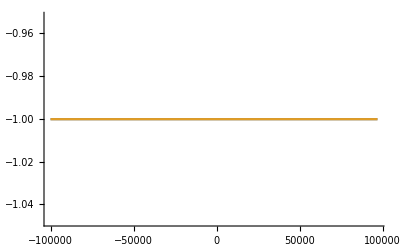

```mathematica
Plot[{-1/2 b^3(-1+3 u0d[0.59,y]^2)//Simplify,a3[t,0,x,y]/.a3Rule/.x->0.59},{y,yValues[[1]],yValues[[-1]]}]
```

Export a3 Initial data

```mathematica
(*a3PertAmpl=10^-4;
a3Pert=Table[0,{i,1,xValues//Length},{j,1,yValues//Length}];
For [l=2, l≤150,l++,
{AAa3,ϕna3,nxa3,nya3}={RandomReal[a3PertAmpl],RandomReal[{0,2π}],RandomInteger[{1,64}],RandomInteger[{1,64}]};
a3Pert=Table[a3Pert[[i,j]]+AAa3 Cos[ϕna3+(2π)/(xMax-xMin)nxa3 xValues[[i]]+(2π)/(xMax-xMin)nya3 yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];]*)
```

```mathematica
(*Max[a3Pert]
Max[Table[(a3[t,0,x,y]/.a3Rule/.x->xValues[[i]]/.y->yValues[[j]]),{i,1,xValues//Length},{j,1,yValues//Length}]]*)
```

```mathematica
a3Data=Table[(a3[t,0,x,y]/.a3Rule/.x->xValues[[i]]/.y->yValues[[j]])(*+a3Pert[[i,j]]*),{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
xiData=Table[(ξ[t,x,y](*/.ξ[t,x,y]->0*)(*1-Hypergeometric2F1[-0.3333333333333333,0.5,0.6666666666666666,-1/2-1/2 Cos[(2223497 y)/5898008975]]*)/.xiRule/.c1Rule/.x->xValues[[i]]/.y->yValues[[j]])(*(1+(RandomReal[]-0.5)/100)*),{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
guessData=Table[N[(uofρRule[[1,2]][b^-1,x,y])^-1/.c1Rule/.x->xValues[[i]]/.y->yValues[[j]],prec]1,{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
guessData[[1,1]]
```

1.00002

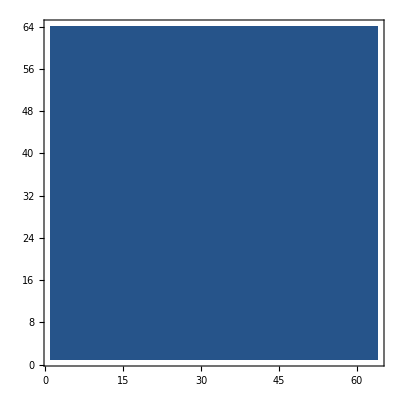

```mathematica
ListContourPlot[a3Data]
```

```mathematica
a3AttributesAndData={"a3"->a3Data};
```

```mathematica
xiAttributesAndData={"xi"->xiData};
```

```mathematica
guessAttributesAndData={"guess"->guessData};
```

```mathematica
Export[IDFolderName<>"Initiala3_BBB.h5",a3AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/SourceInitiala3_BBB.h5

```mathematica
Export[IDFolderName<>"Initialxi_BBB.h5",xiAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/SourceInitialxi_BBB.h5

```mathematica
Export[IDFolderName<>"Initialguess_BBB.h5",guessAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/SourceInitialguess_BBB.h5

#### f1

Same procedure as above but for F1.

```mathematica
FExp=u f1[t,x,y]+Derivative[0,1,0][ξ][t,x,y]+1/4(-4 f1[t,x,y] ξ[t,x,y](*+3 𝒢^(0,0,1)[t,x,y]*)(*+3 𝒫^(0,1,0)[t,x,y]*))u^2;
```

```mathematica
FExpOfρ=FExp/.u->uofρ[ρ,x,y](*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,2}]&
```

ξ^(0,1,0)[t,x,y]+1. f1[t,x,y] ρ-1. (f1[t,x,y] ξ[t,x,y]) ρ^2+O[ρ]^3

Turbulence draft

```mathematica
(*FToMatch=(b ρ)^3/ρ^2 u0d[x,y] u1d[x,y]*)
```

∂_u Fy=

```mathematica
(*Series[D[rofρ[ρ,x,y],ρ],{ρ,0,3}]*)
```

```mathematica
SeriesCoefficient[FExpOfρ,{ρ,0,1}]
SeriesCoefficient[FToMatch,{ρ,0,1}]
```

1. f1[t,x,y]

-0.0100005

Chasler paper

```mathematica
FToMatch=-(b ρ(*ofu[{0,x,y}]*))^3/(ρ(*ofu[{0,x,y}]*))^2 u0d[x,y] u1d[x,y]
```

-0.0100005 ρ

```mathematica
(*Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ]*)
```

```mathematica
SeriesCoefficient[FToMatch,{ρ,0,1}]==SeriesCoefficient[FExpOfρ,{ρ,0,1}]
```

-0.0100005==1. f1[t,x,y]

```mathematica
fxRule=Solve[Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ],f1[t,x,y]]//Simplify
```

{{f1[t,x,y]→-0.0100005}}

From Chasler paper this should be.

```mathematica
(*-u0d[x,y] u1d[x,y]*)
```

```mathematica
1500
```

1500

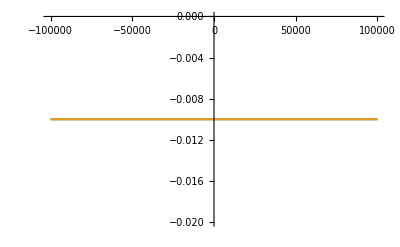

```mathematica
Plot[{- b^3 u0d[1.48,y] u1d[1.48,y],fxRule[[1,1,2]]/.x->1.48},{y,yMin,yMax}]
```

```mathematica
SeriesCoefficient[FToMatch,{ρ,0,0}]
SeriesCoefficient[FExpOfρ,{ρ,0,0}]
```

0

ξ^(0,1,0)[t,x,y]

```mathematica
DSolve[SeriesCoefficient[FToMatch,{ρ,0,0}]==SeriesCoefficient[FExpOfρ,{ρ,0,0}],ξ,{t,x,y}]//Flatten
```

{ξ→Function[{t,x,y},C[1][t,y]]}

```mathematica
DSolve[SeriesCoefficient[FToMatch,{ρ,0,0}]==SeriesCoefficient[FExpOfρ,{ρ,0,2}],ξ,{t,x,y}]//Flatten
```

{ξ→Function[{t,x,y},0.]}

ξ can’t depend on x!

Export fx initial data

```mathematica
(*Maxfx=Maximize[fxRule[[1,1,2]],y][[1]];*)
```

```mathematica
fxPertAmpl=10^-3;
fxPert=Table[0,{i,1,xValues//Length},{j,1,yValues//Length}];
For [l=2, l≤150,l++,
{AAfx,ϕnfx,nxfx,nyfx}={RandomReal[fxPertAmpl],RandomReal[{0,2π}],RandomInteger[{1,64}],RandomInteger[{1,64}]};
fxPert=Table[fxPert[[i,j]]+AAfx Cos[ϕnfx+(2π)/(xMax-xMin)nxfx xValues[[i]]+(2π)/(xMax-xMin)nyfx yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];]
```

```mathematica
fxData=Table[((f1[t,x,y]/.fxRule[[1]])/.x->xValues[[i]]/.y->yValues[[j]])+fxPert[[i,j]],{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
fxData//Dimensions
```

{64,64}

```mathematica
Max[fxPert]/Max[Table[((f1[t,x,y]/.fxRule[[1]])/.x->xValues[[i]]/.y->yValues[[j]]),{i,1,xValues//Length},{j,1,yValues//Length}]]
```

-1.77801

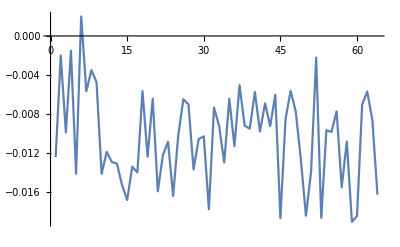

```mathematica
ListPlot[fxData[[1]],Joined->True]
```

```mathematica
fxAttributesAndData={"fx"->fxData};
```

```mathematica
Export[IDFolderName<>"Initialfx_BBB.h5",fxAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/SourceInitialfx_BBB.h5

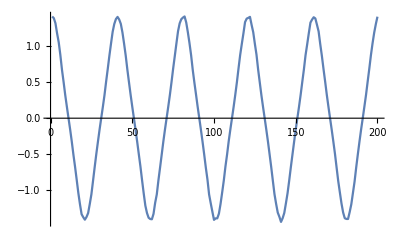

```mathematica
ListPlot[Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5","Data"][[1,1]],Joined->True,PlotRange->All]
```

#### f2

Same procedure as above but for F1.

```mathematica
F2Exp=u f2[t,z,y]+Derivative[0,0,1][ξ][t,x,y];
```

```mathematica
F2ExpOfρ=F2Exp/.u->uofρ[ρ,x,y]^1(*/.c1Rule*)(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,4}]&;
```

Turbulence draft

```mathematica
(*FToMatch=(b ρ)^3/ρ^2 u0d[x,y] u1d[x,y]*)
```

∂_u Fy=

```mathematica
(*Series[D[rofρ[ρ,x,y],ρ],{ρ,0,3}]*)
```

Chasler paper

```mathematica
F2ToMatch=-(b ρ(*ofu[{0,x,y}]*))^3/(ρ(*ofu[{0,x,y}]*))^2 u0d[x,y] u2d[x,y];
```

```mathematica
(*Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ]*)
```

```mathematica
fyRule=Solve[Coefficient[F2ToMatch,ρ]==Coefficient[F2ExpOfρ,ρ],f2[t,z,y]]//Simplify
```

{{f2[t,z,y]→0.}}

From Chasler paper this should be.

```mathematica
(*-u0d[x,y] u1d[x,y]*)
```

```mathematica
fyRule[[1,1,2]]/.x->148/.y->-50000
fyRule[[1,1,2]]/.x->148/.y->50000
```

0.

0.

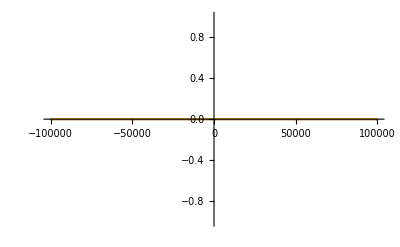

```mathematica
Plot[{-u0d[1.48,y] u2d[1.48,y],fyRule[[1,1,2]]/.x->1.48},{y,yMin,yMax}]
```

```mathematica
DSolve[SeriesCoefficient[F2ToMatch,{ρ,0,0}]==SeriesCoefficient[F2ExpOfρ,{ρ,0,0}],ξ,{t,x,y}]//Flatten
```

{ξ→Function[{t,x,y},C[1][t,x]]}

ξ can’t depend on x!

Export fx initial data

```mathematica
fyPertAmpl= 10^-3;
fyPert=Table[0,{i,1,xValues//Length},{j,1,yValues//Length}];
For [l=2, l≤100,l++,
{AAfy,ϕnfy,nxfy,nyfy}={RandomReal[fyPertAmpl],RandomReal[{0,2π}],RandomInteger[{1,64}],RandomInteger[{1,64}]};
fyPert=Table[fyPert[[i,j]]+AAfy Cos[ϕnfy+(2π)/(xMax-xMin)nxfy xValues[[i]]+(2π)/(yMax-yMin)nyfy yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];]
```

```mathematica
fyData=Table[((f2[t,z,y]/.fyRule[[1]])/.x->xValues[[i]]/.y->yValues[[j]])1+fyPert[[i,j]],{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
Max[fyData]
```

0.0135027

```mathematica
Norm[fyData]
```

0.0661041

```mathematica
0.006967497791432687
```

0.0069675

```mathematica
(*fxRule*)
```

```mathematica
fyData//Dimensions
```

{64,64}

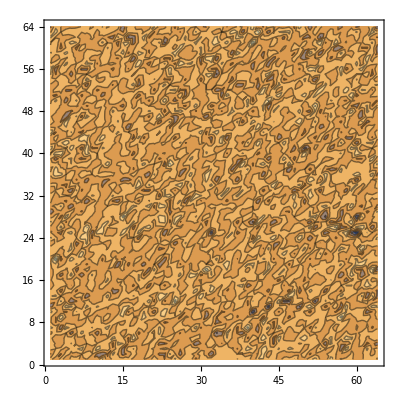

```mathematica
ListContourPlot[fyData]
```

```mathematica
fyAttributesAndData={"fy"->fyData};
```

```mathematica
Export[IDFolderName<>"Initialfy_BBB.h5",fyAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/SourceInitialfy_BBB.h5

```mathematica
(*Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5","Data"]*)
```

### B Function

#### Grid For ρ

The initial data for B is different, since B is defined through the entire domain. We need to invert the function r(ρ). This is a problem, since that is not invertible analytically.

```mathematica
(*ClearAll[uofρ]*)
```

```mathematica
(*uofρ=Function[{ρs,xs,ys},uofρ/.c1Rule[[1]](*/.ξ->Function[{t,x,y},0]*)/.ρ->ρs/.x->xs/.y->ys]*)
```

```mathematica
(*uofρ[ρs_,xs_,ys_]:=rofρ[[2]]^-1/.c1Rule[[1]]/.ξ->Function[{t,x,y},0]/.ρ->ρs/.x->xs/.y->ys*)
```

```mathematica
(*uofρ=Function[{ρs,xs,ys},uofρ^-1/.c1Rule[[1]]/.ξ->Function[{t,x,y},0]/.ρ->ρs/.x->xs/.y->ys]*)
```

Horizon location

```mathematica
(*rofρ2=r/.DSolve[{D[r[ρ,x,y],{ρ}]==(-1/ρ^2(1+((*b[x,y]*)b ρ)^3(u1d[x,y]^2+u2d[x,y]^2))^(-1/2)),r[1,x,y]==1},r,{ρ,x,y}]//Flatten*)
```

```mathematica
Plot3D[uofρ[b^-1,x,y](*/.b[x,y]->1*)/.c1Rule,{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
Maximize[uofρ[b^-1,x,y],{x,y(*,xMin,xMax*)}][[1]]//FullForm
Minimize[uofρ[b^-1,x,y],{x,y(*,xMin,xMax*)}][[1]]//FullForm
```

0.999975

0.999975

```mathematica
(*uofρToInt=ParallelTable[{MyGrid[[i,j,k]],uofρ[MyGrid[[i,j,k]][[1]],MyGrid[[i,j,k]][[2]],MyGrid[[i,j,k]][[3]]]},{i,1,MyGrid//Length},{j,1,MyGrid[[1]]//Length},{k,1,MyGrid[[1,1]]//Length}];//AbsoluteTiming*)
```

```mathematica
(*ρofuOld2=InverseFunction[Function[{ρ,x,y},Intuofρ[ρ,x,y]],1,3];*)
```

```mathematica
ρofuOld=InverseFunction[Function[{ρ,x,y},uofρ[ρ,x,y]],1,3];
```

```mathematica
ClearAll[ρofu,ρofu2]
```

```mathematica
ρofu=Function[C,ρofuOld[C[[1]],C[[2]],C[[3]]]]
```

Function[C,ρofuOld[C⟦1⟧,C⟦2⟧,C⟦3⟧]]

```mathematica
ρofu[MyGrid[[2,1,1,1]]]//N//AbsoluteTiming
```

{0.002427,0.1}

```mathematica
ρofuValues=ParallelTable[ρofu[MyGrid[[n,i,j,k]]],{n,1,uValues//Length},{i,1,uValues[[n]]//Length},{j,1,xValues//Length},{k,1,yValues//Length}];//AbsoluteTiming
```

{88.7375,Null}

```mathematica
u1Values=Table[u1d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.007396,Null}

```mathematica
u2Values=Table[u2d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.004166,Null}

```mathematica
u0Values=Table[u0d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{2.08537,Null}

#### B Function

```mathematica
ClearAll[InitialBAnalytic]
```

```mathematica
InitialBAnalytic[u_,x_,y_]:=-1/2 Log[(1+(b ρofu[{u,x,y}])^3 u1d[x,y]^2)/(1+(b ρofu[{u,x,y}])^3 u2d[x,y]^2)] u^-3;
```

```mathematica
InitialB1=ParallelTable[N[SeriesCoefficient[InitialBAnalytic[u,xValues[[i]],yValues[[j]]],{u,uValues[[1,1]],0}]//Normal](*(1+10^-4( RandomReal[]-0.5))*),{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming
```

{40.3688,Null}

```mathematica
InitialB=ParallelTable[N[-1/2 Log[(1+(b ρofuValues[[n,ui,xi,yi]])^3 u1Values[[xi,yi]]^2)/(1+(b ρofuValues[[n,ui,xi,yi]])^3 u2Values[[xi,yi]]^2)] uValues[[n,ui]]^-3,$MinPrecision](*(1+(RandomReal[]-0.5)/10^4)*),{n,1,uValues//Length},{ui,1,uValues[[n]]//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming
InitialB[[1,1]]=InitialB1(*Table[-0.5,{i,1,25},{j,1,25}]*);
(*InitialB[[1]]=InitialB[[2]];*)
```

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^3 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{1.17129,Null}

```mathematica
ExportAttributes=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndData=Table[ExportAttributes[[i]]->InitialB[[i]],{i,1,ExportAttributes//Length}];//AbsoluteTiming
```

{0.017487,Null}

```mathematica
Export[IDFolderName<>"InitialB_BBB.h5",AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/SourceInitialB_BBB.h5

#### G Function

```mathematica
ArcSinh[(b^3 u1 u2 ρ^3)/(√(1+b^3 (u1^2+u2^2) ρ^3))]//TrigToExp//Together//Simplify
```

Log[(u1 u2 ρ^3)/(√(1+(u1^2+u2^2) ρ^3))+√(1+(u1^2 u2^2 ρ^6)/(1+(u1^2+u2^2) ρ^3))]

```mathematica
InitialG=ParallelTable[N[ArcSinh[(b^3 u1Values[[xi,yi]] u2Values[[xi,yi]] ρofuValues[[n,ui,xi,yi]]^3)/(√(1+b^3 (u1Values[[xi,yi]]^2+u2Values[[xi,yi]]^2) ρofuValues[[n,ui,xi,yi]]^3))](*Log[(b^3 u1Values[[n,ui]] u2Values[[xi,yi]] ρofuValues[[n,ui,xi,yi]]^3+√((1+b^3 uValues[[n,ui]]^2 ρofuValues[[n,ui,xi,yi]]^3) (1+b^3 u2Values[[xi,yi]]^2 ρofuValues[[n,ui,xi,yi]]^3)))/(√(1+b^3 (uValues[[n,ui]]^2+u2Values[[xi,yi]]^2) ρofuValues[[n,ui,xi,yi]]^3))]*)uValues[[n,ui]]^-3,$MinPrecision](*+((RandomReal[]-0.5)/10^4)*),{n,1,uValues//Length},{ui,1,uValues[[n]]//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming
```

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^3 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{0.880223,Null}

```mathematica
InitialGAnalytic[u_,x_,y_]:=ArcSinh[(b^3 u1d[x,y] u2d[x,y] ρofu[{u,x,y}]^3)/(√(1+b^3 (u1d[x,y]^2+u2d[x,y]^2) ρofu[{u,x,y}]^3))](*Log[(b^3 u1d[x,y] u2d[x,y] ρofu[{u,x,y}]^3+√((1+b^3 u1d[x,y]^2 ρofu[{u,x,y}]^3) (1+b^3 u2d[x,y]^2 ρofu[{u,x,y}]^3)))/(√(1+b^3 (u1d[x,y]^2+u2d[x,y]^2) ρofu[{u,x,y}]^3))]*)u^-3;
```

```mathematica
InitialG1=ParallelTable[N[SeriesCoefficient[InitialGAnalytic[u,xValues[[i]],yValues[[j]]],{u,uValues[[1,1]],0}]//Normal],{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming
InitialG[[1,1]]=InitialG1;
```

{0.090096,Null}

```mathematica
InitialG//Flatten//Im//Norm
```

0

```mathematica
InitialG[[1,1,;;,;;]]//ListPlot3D
```

-Graphics3D-

```mathematica
ExportAttributesG=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndDataG=Table[ExportAttributesG[[i]]->(InitialG[[i]]//Re),{i,1,ExportAttributesG//Length}];//AbsoluteTiming
```

{0.064714,Null}

```mathematica
Export[IDFolderName<>"InitialG_BBB.h5",AttributesAndDataG,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/SourceInitialG_BBB.h5

### Source Function

```mathematica
S0[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_]:=(1+(1+Tanh[(t-t0)/tau])A  1/((sigmax )^2 2Pi)Exp[(-( x (2Pi)/L-x0)^2)/(2 (sigmax )^2)] 1/((sigmay )^2 2Pi)Exp[(-( y (2Pi)/L-y0)^2)/(2 (sigmay )^2)])^(-1/2);
```

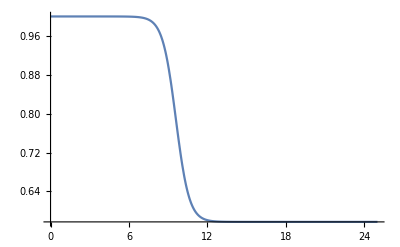

```mathematica
Plot[(1+(1+Tanh[(t-t0)/tau]))^(-1/2)/.tau->1/.t0->10,{t,0,25},PlotRange->All]
```

```mathematica
1-(2+Tanh[(t-t0)/tau])^(-1/2)/.tau->1/.t0->15/.t->0//N
```

9.34808×10^-14

```mathematica
Maximize[S0[0,t0test,tautest,Atest,x,x0test,sigmaxtest,y,y0test,sigmaytest]/.L->20^5,{x,y}]
Minimize[S0[0,t0test,tautest,Atest,x,x0test,sigmaxtest,y,y0test,sigmaytest]/.L->20^5,{x,y}]
```

Maximize[1/(√(1+(Atest ⅇ^(-((π x)/1600000-x0test)^2/(2 sigmaxtest^2)-((π y)/1600000-y0test)^2/(2 sigmaytest^2)) (1-Tanh[t0test/tautest]))/(4 π^2 sigmaxtest^2 sigmaytest^2))),{x,y}]

Minimize[1/(√(1+(Atest ⅇ^(-((π x)/1600000-x0test)^2/(2 sigmaxtest^2)-((π y)/1600000-y0test)^2/(2 sigmaytest^2)) (1-Tanh[t0test/tautest]))/(4 π^2 sigmaxtest^2 sigmaytest^2))),{x,y}]

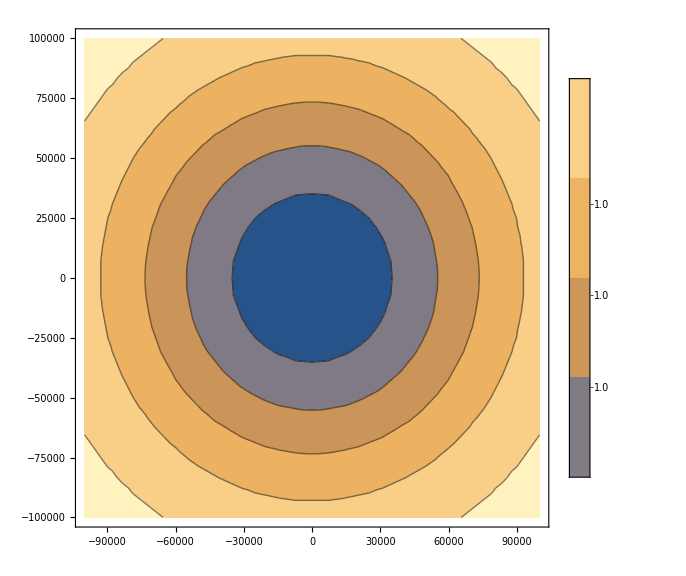

```mathematica
t0test=15;
tautest=1;
Atest=0.006;
sigmaxtest= 0.125;
sigmaytest=0.125;
x0test=0;
y0test=0;

ContourPlot[S0[0,t0test,tautest,Atest,x,x0test,sigmaxtest,y,y0test,sigmaytest]/.L->20^5,{x,-10^5,10^5},{y,-10^5,10^5},PlotRange->All,PlotLegends->Automatic,ImageSize->Large]
```

```mathematica
rules={A->GS[Amp],L->GS[L],x0->GS[x0],y0->GS[y0],sigmax->GS[sigmax],sigmay->GS[sigmay],t0->GS[t0],tau->GS[tau]}
```

{A→GS[Amp],L→GS[L],x0→GS[x0],y0→GS[y0],sigmax→GS[sigmax],sigmay→GS[sigmay],t0→GS[t0],tau→GS[tau]}

```mathematica
expr=S0[t,t0,tau,A,x,x0,sigmax,y,y0,sigmay(*,{x,1},{y,1}*)]//FullSimplify
```

1/(√(1+(A ⅇ^(-((-2 π x+L x0)^2/sigmax^2+(-2 π y+L y0)^2/sigmay^2)/(2 L^2)) (1+Tanh[(t-t0)/tau]))/(4 π^2 sigmax^2 sigmay^2)))

```mathematica
newExpr=expr/. rules//Simplify//FortranForm;
(*First,replace GS(...) safely*)expr1=StringReplace[ToString[newExpr],"GS("~~(param:(LetterCharacter|DigitCharacter)..)~~")":>"GS."<>param];
(*Then,process exponentiation and other fixes separately*)
expr2=StringReplace[expr1,{"E**"->"MathConstants.e^"}];
expr3=StringReplace[expr2,{"**"->"^"}];
expr4=StringReplace[expr3,{"**"->"^",(*Fix power notation after GS replacement*)"e"~~(x:DigitCharacter..):>"e"<>x,(*Fix scientific notation*)x:(DigitCharacter..)~~"."~~(y:Except[DigitCharacter]..):>x<>y,(*Remove unnecessary dots*)"Pi"->"pi",(*Mathematica uses'Pi',Julia uses'pi'*)"Tanh"->"tanh"}];
```

```mathematica
expr3//Print
```

1/Sqrt(1 + (GS.Amp*(1 + Tanh((t - GS.t0)/GS.tau)))/(4.*MathConstants.e^(((-2*Pi*x + GS.L*GS.x0)^2/GS.sigmax^2 + (-2*Pi*y + GS.L*GS.y0)^2/GS.sigmay^2)/(2.*GS.L^2))*Pi^2*GS.sigmax^2*GS.sigmay^2))

```mathematica
SetOptions[$Output,PageWidth->Infinity];

(*Define the function Sz*)
Sz[t_,x_,y_]:=S0[t,t0,tau,A,x,x0,sigmax,y,y0,sigmay]; (*Replace'expr' with your actual function*)

(*Compute derivatives*)
Szx[t_,x_,y_]=D[Sz[t,x,y],x];
Szxx[t_,x_,y_]=D[Szx[t,x,y],x];
Szxxx[t_,x_,y_]=D[Szxx[t,x,y],x];
Szxxxx[t_,x_,y_]=D[Szxxx[t,x,y],x];

Szy[t_,x_,y_]=D[Sz[t,x,y],y];
Szxy[t_,x_,y_]=D[Szx[t,x,y],y];
Szxxy[t_,x_,y_]=D[Szxx[t,x,y],y];
Szxyy[t_,x_,y_]=D[Szxy[t,x,y],y];
Szxxyy[t_,x_,y_]=D[Szxxy[t,x,y],y];

Szyy[t_,x_,y_]=D[Szy[t,x,y],y];
Szyyy[t_,x_,y_]=D[Szyy[t,x,y],y];
Szyyyy[t_,x_,y_]=D[Szyyy[t,x,y],y];

Szt[t_,x_,y_]=D[Sz[t,x,y],t];
Sztx[t_,x_,y_]=D[Szt[t,x,y],x];
Szty[t_,x_,y_]=D[Szt[t,x,y],y];
Sztxx[t_,x_,y_]=D[Sztx[t,x,y],x];
Sztyy[t_,x_,y_]=D[Szty[t,x,y],y];
Sztxy[t_,x_,y_]=D[Sztx[t,x,y],y];


(*Function to process expressions*)
processExpression[expr_]:=Module[{newExpr,expr1,expr2,expr3,expr4},newExpr=expr/. rules//Simplify//FortranForm;
expr1=StringReplace[ToString[newExpr],"GS("~~(param:(LetterCharacter|DigitCharacter)..)~~")":>"GS."<>param];
expr2=StringReplace[expr1,{"E**"->"MathConstants.e^"}];
expr3=StringReplace[expr2,{"**"->"^"}];
expr4=StringReplace[expr3,{"Pi"->"pi"}];
expr5=StringReplace[expr4,{"**"->"^","e"~~(x:DigitCharacter..):>"e"<>x,x:(DigitCharacter..)~~"."~~(y:Except[DigitCharacter]..):>x<>y,"Pi"->"pi","Tanh"->"tanh","Sech"->"sech","Sqrt"->"sqrt","Sinh"->"sinh","Cosh"->"cosh"}];
expr5];

(*Process all expressions*)
expressions={"Sz(t, x, y, GS ::GaussianSource) = "<>processExpression[Sz[t,x,y]],"Sz_x(t, x, y, GS ::GaussianSource) = "<>processExpression[Szx[t,x,y]],"Sz_xx(t, x, y, GS ::GaussianSource) = "<>processExpression[Szxx[t,x,y]],"Sz_xxx(t, x, y, GS ::GaussianSource) = "<>processExpression[Szxxx[t,x,y]],"Sz_xxxx(t, x, y, GS ::GaussianSource) = "<>processExpression[Szxxxx[t,x,y]],"Sz_y(t, x, y, GS ::GaussianSource) = "<>processExpression[Szy[t,x,y]],"Sz_xy(t, x, y, GS ::GaussianSource) = "<>processExpression[Szxy[t,x,y]],"Sz_xxy(t, x, y, GS ::GaussianSource) = "<>processExpression[Szxxy[t,x,y]],"Sz_xyy(t, x, y, GS ::GaussianSource) = "<>processExpression[Szxyy[t,x,y]],"Sz_xxyy(t, x, y, GS ::GaussianSource) = "<>processExpression[Szxxyy[t,x,y]],"Sz_yy(t, x, y, GS ::GaussianSource) = "<>processExpression[Szyy[t,x,y]],"Sz_yyy(t, x, y, GS ::GaussianSource) = "<>processExpression[Szyyy[t,x,y]],"Sz_yyyy(t, x, y, GS ::GaussianSource) = "<>processExpression[Szyyyy[t,x,y]],"Sz_t(t, x, y, GS ::GaussianSource) = "<>processExpression[Szt[t,x,y]],"Sz_tx(t, x, y, GS ::GaussianSource) = "<>processExpression[Sztx[t,x,y]],"Sz_ty(t, x, y, GS ::GaussianSource) = "<>processExpression[Szty[t,x,y]],"Sz_txx(t, x, y, GS ::GaussianSource) = "<>processExpression[Sztxx[t,x,y]],"Sz_tyy(t, x, y, GS ::GaussianSource) = "<>processExpression[Sztyy[t,x,y]],"Sz_txy(t, x, y, GS ::GaussianSource) = "<>processExpression[Sztxy[t,x,y]]};

(*Export to file*)
Export["/home/giulio/University/PhD/translated_expressions.txt",expressions,"Text"];
```